```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
```

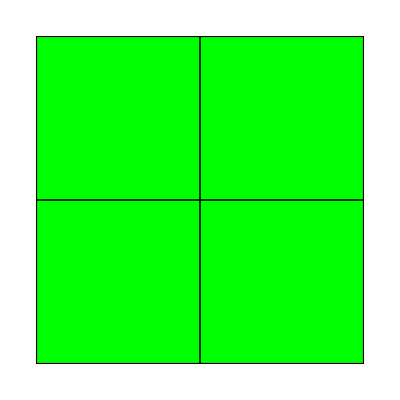

```mathematica
(*Uvozimo elemente ter node*)
Elements = Import["Data4ele/elements4.txt","Table","FieldSeparators"->","];
Nodes = Import["Data4ele/nodes4.txt","Table","FieldSeparators"->","];
Nodes = Drop[Nodes, None, {1}];(*odstrani prvi stolpec*)
Elements = Drop[Elements, None, {1}];

(*Prikaz elementov*)
ELplot= Table[{
	Graphics[{Green,EdgeForm[Black],Polygon[Nodes[[Elements[[i]]]]]}]},
	{i,1,Length[Elements]}];
Show[ELplot]
```

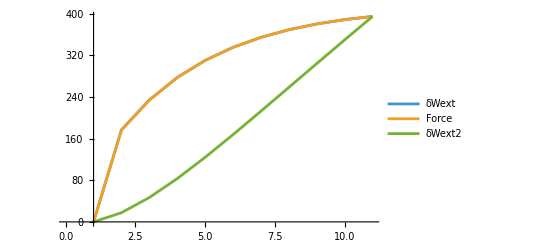

```mathematica
(*Uvoz podatkov -> Sila*)
Force = Import["Data4ele/Sila_4ele.txt", "Table", HeaderLines -> 3][[1;;-5,2]];
δWext = 1 * Force;
(*Pomiki ter napetosti*)
U = Import["Data4ele/Pomiki_4ele.txt", "Table", HeaderLines -> 3][[1;;-5, 2]];
δWext2 = Force U;

ListLinePlot[{δWext, Force, δWext2}, AxesOrigin->{1,0}, PlotLegends->{"δWext","Force" ,"δWext2"}]
```

```mathematica
(*Uvoz napesti -> kot gradient*)
NAP = Import["Data4ele/Napetost.JSON", "RawJSON"];
```

```mathematica
(*Uvoz gradientov*)
(*FJSON[frame][element][Gauss Integration Point][Variable -> x,y,F]*)
(*F = FJSON[ToString[frame]][ToString[element]][ToString[integracijsaTocka]]["F"];*)
FJSON = Import["Data4ele/Grad_4ele_PHANTOM.json","RawJSON"];
```

```mathematica
(*Iteracija po framih*)
Frames = Length[Keys[FJSON]];
Frames = 10;
nelements = Length[Keys[FJSON[["1"]]]];
ngpoint = Length[Keys[FJSON[["1"]][[ToString[Keys[FJSON[["1"]]][[1]]]]]]];
Δt = 1/(Frames-1) (Frames-1) ;
```

```mathematica
δWint = {}; (*Notranje virtualno delo za vse frame*)
(*Jacobian matrix*)
(*Mapping the determinant*)


For[frame = 1, frame <= Frames+1, frame ++,
det = {};
Subscript[𝒯, 1] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {-1,-1};
Subscript[𝒯, 2] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {1,-1};
Subscript[𝒯, 3] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {1,1};
Subscript[𝒯, 4] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {-1,1};
Subscript[ψ, i_][𝒳_, 𝒴_] := 1/4(1 + Subscript[𝒯, i][[1]] * 𝒳) *(1 + Subscript[𝒯, i][[2]]  * 𝒴);


For[j =1, j <= Length[Elements], j++,
	x = Nodes[[Elements[[j]]]][[;;,1]];
	y = Nodes[[Elements[[j]]]][[;;,2]];

	X[𝒳_, 𝒴_]  := Sum[Subscript[ψ, i][𝒳, 𝒴] x[[i]],{i,1,4}];
	Y[𝒳_, 𝒴_]  := Sum[Subscript[ψ, i][𝒳, 𝒴] y[[i]],{i,1,4}];
	J[𝒳_, 𝒴_]  = ({{D[X[𝒳, 𝒴], 𝒳], D[Y[𝒳, 𝒴], 𝒳]}, {D[X[𝒳, 𝒴], 𝒴], D[Y[𝒳, 𝒴], 𝒴]}});
	(*J[𝒳_, 𝒴_] = ({{D[X[𝒳, 𝒴],𝒳], D[Y[𝒳, 𝒴],𝒳]}, {D[X[𝒳, 𝒴],𝒴], D[Y[𝒳, 𝒴],𝒴]}});*)
];
det = Append[det,
{
Det[J[-1/(√3),-1/(√3)]],
Det[J[1/(√3),-1/(√3)]],
Det[J[-1/(√3),1/(√3)]],
Det[J[1/(√3),1/(√3)]]
}
];

(*
1. For -> index ele -> elementi
	2. For -> index gp -> integrac. tocka
*)
Fframe = FJSON[ ToString[frame-1]];
ElementNumbers = Keys[FJSON[[1]]];
δWinte = 0;
For[ele=1, ele <= Length[Elements], ele++,
nele2 =  Keys[FJSON[["1"]]][[ele]];
Fele = Fframe[ ToString[nele2]];
δWintgp = 0;

For[gp = 1, gp <= 4, gp++,
(*	Print["frame -> ",frame, " N. ele -> ",ele, " gp -> ",gp]; 
	Print[NAP[[ToString[frame]]][[ToString[ele]]][[ToString[gp]]][["S"]]];
	Print["Grad:  ele ", Fele[[ToString[gp]]]["F"]];*)
	
	F =  Fele[[ToString[gp]]]["F"];
	F11 = F[[1]];
	F12 = F[[2]];
	F21 = F[[3]];
	F22 = F[[4]];
	F33 = F[[5]];
	(*Napetosti*)
	σ = NAP[[ToString[frame-1]]][[ToString[ele]]][[ToString[gp]]][["S"]];
	(*σ -> S11, S22, S33, S12*)
	σ11 =σ[[1]];
	σ12 =σ[[4]]; (*Drugi stolpec*)
	σ22 =σ[[3]];
	
	(*δv -> Ḟ*)
	Fdot =FJSON[ToString[Keys[FJSON][[-1]]]][ToString[ElementNumbers[[ele]]]][ToString[gp]]["F"];
	δvf = 1/Δt (Fdot - {1,1,1,1,1});
	(*Print[δvf];*)
	δv11 = δvf[[1]];
	δv12 = δvf[[2]];
	δv21 = δvf[[3]];
	δv22 = δvf[[4]];
	δv33 = δvf[[5]];

			
	(*1. Piola-Kirchoff Stress -> p*)
	p11 = F33 (F22 σ11 - F12 σ12);
	p12 = - F21 F33 σ11 + F11 F33 σ12;
	p21 = F33 (F22 σ12 - F12 σ22);
	p22 = -F21 F22 σ12 + F11 F33 σ22;
			

	(*Print[δWinti]*)
	δW = (p11 δv11 + p12 δv12 + p21 δv21 + p22 δv22) *det[[1,gp]];
	δWintgp += δW; (*Sum dela vseh gaussovih tock*) 
	];
	δWinte += δWintgp;
];
δWint = Append[δWint, δWinte];
(*kako je z delom, ali ga je treba pomnoziti z stevilom elemenov*)
];
```

δWintgp ->1 0.

δWintgp ->2 0.

δWintgp ->3 0.

δWintgp ->4 0.

δWinte ->1 0.

δWintgp ->1 0.

δWintgp ->2 0.

δWintgp ->3 0.

δWintgp ->4 0.

δWinte ->2 0.

δWintgp ->1 0.

δWintgp ->2 0.

δWintgp ->3 0.

δWintgp ->4 0.

δWinte ->3 0.

δWintgp ->1 0.

δWintgp ->2 0.

δWintgp ->3 0.

δWintgp ->4 0.

δWinte ->4 0.

δWintgp ->1 11.0378

δWintgp ->2 22.0756

δWintgp ->3 33.1133

δWintgp ->4 44.1511

δWinte ->1 44.1511

δWintgp ->1 11.0378

δWintgp ->2 22.0756

δWintgp ->3 33.1133

δWintgp ->4 44.1511

δWinte ->2 88.3022

δWintgp ->1 11.0378

δWintgp ->2 22.0756

δWintgp ->3 33.1133

δWintgp ->4 44.1511

δWinte ->3 132.453

δWintgp ->1 11.0378

δWintgp ->2 22.0756

δWintgp ->3 33.1133

δWintgp ->4 44.1511

δWinte ->4 176.604

δWintgp ->1 14.6254

δWintgp ->2 29.2509

δWintgp ->3 43.8763

δWintgp ->4 58.5018

δWinte ->1 58.5018

δWintgp ->1 14.6254

δWintgp ->2 29.2509

δWintgp ->3 43.8763

δWintgp ->4 58.5018

δWinte ->2 117.004

δWintgp ->1 14.6254

δWintgp ->2 29.2509

δWintgp ->3 43.8763

δWintgp ->4 58.5018

δWinte ->3 175.505

δWintgp ->1 14.6254

δWintgp ->2 29.2509

δWintgp ->3 43.8763

δWintgp ->4 58.5018

δWinte ->4 234.007

δWintgp ->1 17.3279

δWintgp ->2 34.6558

δWintgp ->3 51.9838

δWintgp ->4 69.3117

δWinte ->1 69.3117

δWintgp ->1 17.3279

δWintgp ->2 34.6558

δWintgp ->3 51.9838

δWintgp ->4 69.3117

δWinte ->2 138.623

δWintgp ->1 17.3279

δWintgp ->2 34.6558

δWintgp ->3 51.9838

δWintgp ->4 69.3117

δWinte ->3 207.935

δWintgp ->1 17.3279

δWintgp ->2 34.6558

δWintgp ->3 51.9838

δWintgp ->4 69.3117

δWinte ->4 277.247

δWintgp ->1 19.3808

δWintgp ->2 38.7616

δWintgp ->3 58.1424

δWintgp ->4 77.5232

δWinte ->1 77.5232

δWintgp ->1 19.3808

δWintgp ->2 38.7616

δWintgp ->3 58.1424

δWintgp ->4 77.5232

δWinte ->2 155.046

δWintgp ->1 19.3808

δWintgp ->2 38.7616

δWintgp ->3 58.1424

δWintgp ->4 77.5232

δWinte ->3 232.57

δWintgp ->1 19.3808

δWintgp ->2 38.7616

δWintgp ->3 58.1424

δWintgp ->4 77.5232

δWinte ->4 310.093

δWintgp ->1 20.9481

δWintgp ->2 41.8961

δWintgp ->3 62.8442

δWintgp ->4 83.7923

δWinte ->1 83.7923

δWintgp ->1 20.9481

δWintgp ->2 41.8961

δWintgp ->3 62.8442

δWintgp ->4 83.7923

δWinte ->2 167.585

δWintgp ->1 20.9481

δWintgp ->2 41.8961

δWintgp ->3 62.8442

δWintgp ->4 83.7923

δWinte ->3 251.377

δWintgp ->1 20.9481

δWintgp ->2 41.8961

δWintgp ->3 62.8442

δWintgp ->4 83.7923

δWinte ->4 335.169

δWintgp ->1 22.1464

δWintgp ->2 44.2929

δWintgp ->3 66.4393

δWintgp ->4 88.5857

δWinte ->1 88.5857

δWintgp ->1 22.1464

δWintgp ->2 44.2929

δWintgp ->3 66.4393

δWintgp ->4 88.5857

δWinte ->2 177.171

δWintgp ->1 22.1464

δWintgp ->2 44.2929

δWintgp ->3 66.4393

δWintgp ->4 88.5857

δWinte ->3 265.757

δWintgp ->1 22.1464

δWintgp ->2 44.2929

δWintgp ->3 66.4393

δWintgp ->4 88.5857

δWinte ->4 354.343

δWintgp ->1 23.0608

δWintgp ->2 46.1215

δWintgp ->3 69.1823

δWintgp ->4 92.2431

δWinte ->1 92.2431

δWintgp ->1 23.0608

δWintgp ->2 46.1215

δWintgp ->3 69.1823

δWintgp ->4 92.2431

δWinte ->2 184.486

δWintgp ->1 23.0608

δWintgp ->2 46.1215

δWintgp ->3 69.1823

δWintgp ->4 92.2431

δWinte ->3 276.729

δWintgp ->1 23.0608

δWintgp ->2 46.1215

δWintgp ->3 69.1823

δWintgp ->4 92.2431

δWinte ->4 368.972

δWintgp ->1 23.7538

δWintgp ->2 47.5077

δWintgp ->3 71.2615

δWintgp ->4 95.0154

δWinte ->1 95.0154

δWintgp ->1 23.7538

δWintgp ->2 47.5077

δWintgp ->3 71.2615

δWintgp ->4 95.0154

δWinte ->2 190.031

δWintgp ->1 23.7538

δWintgp ->2 47.5077

δWintgp ->3 71.2615

δWintgp ->4 95.0154

δWinte ->3 285.046

δWintgp ->1 23.7538

δWintgp ->2 47.5077

δWintgp ->3 71.2615

δWintgp ->4 95.0154

δWinte ->4 380.061

δWintgp ->1 24.2729

δWintgp ->2 48.5457

δWintgp ->3 72.8186

δWintgp ->4 97.0914

δWinte ->1 97.0914

δWintgp ->1 24.2729

δWintgp ->2 48.5457

δWintgp ->3 72.8186

δWintgp ->4 97.0914

δWinte ->2 194.183

δWintgp ->1 24.2729

δWintgp ->2 48.5457

δWintgp ->3 72.8186

δWintgp ->4 97.0914

δWinte ->3 291.274

δWintgp ->1 24.2729

δWintgp ->2 48.5457

δWintgp ->3 72.8186

δWintgp ->4 97.0914

δWinte ->4 388.366

δWintgp ->1 24.6538

δWintgp ->2 49.3076

δWintgp ->3 73.9613

δWintgp ->4 98.6151

δWinte ->1 98.6151

δWintgp ->1 24.6538

δWintgp ->2 49.3076

δWintgp ->3 73.9613

δWintgp ->4 98.6151

δWinte ->2 197.23

δWintgp ->1 24.6538

δWintgp ->2 49.3076

δWintgp ->3 73.9613

δWintgp ->4 98.6151

δWinte ->3 295.845

δWintgp ->1 24.6538

δWintgp ->2 49.3076

δWintgp ->3 73.9613

δWintgp ->4 98.6151

δWinte ->4 394.46

```mathematica
δWint
```

{0.,176.604,234.007,277.247,310.093,335.169,354.343,368.972,380.061,388.366,394.46}

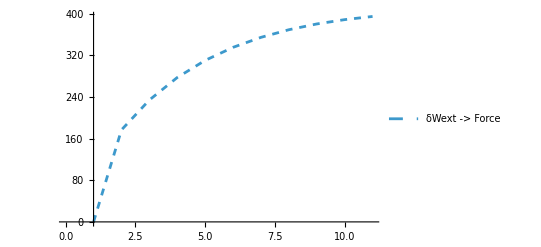

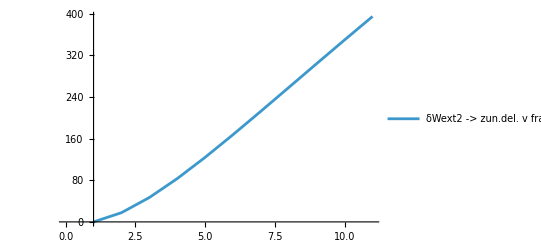

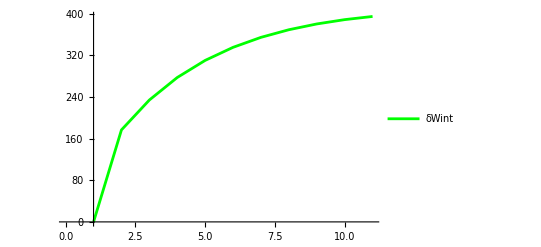

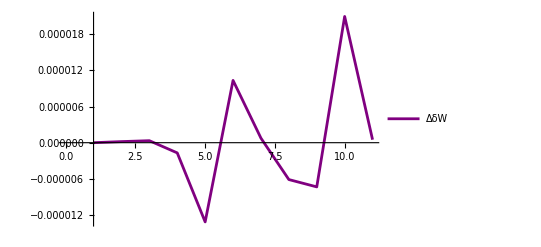

```mathematica
ListLinePlot[{δWext, δWext2, δWint},AxesOrigin->{1,0}, PlotLegends->{"δWext","δWext2","δWint"}, PlotStyle->{Dashed, Dashed, Red}];

P1 = ListLinePlot[{δWext},AxesOrigin->{1,0}, PlotLegends->{"δWext -> Force"}, PlotStyle->Dashed]
P2 = ListLinePlot[{ δWext2},AxesOrigin->{1,0}, PlotLegends->{"δWext2 -> zun.del. v frame"}, PlotStyle->{Normal, Blue}]
P3 = ListLinePlot[{ δWint},AxesOrigin->{1,0}, PlotLegends->{"δWint"}, PlotStyle->Green]
P4 = ListLinePlot[{(δWext - δWint)},AxesOrigin->{1,0}, PlotLegends->{"ΔδW"}, PlotStyle->Purple]
```

```mathematica
{Nap // MatrixForm , U// MatrixForm ,Force // MatrixForm}
```

{Nap,(0.
0.1
0.2
0.3
0.4
0.5
0.6
0.7
0.8
0.9
1.),(0.
176.604
234.007
277.247
310.093
335.169
354.343
368.972
380.061
388.366
394.46)}

```mathematica
{Length[Force],Length[U],Length[Nap],Length[δv]}
```

{11,11,0,0}

```mathematica
Keys[FJSON]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
{δWext,δWext2, δWint}
```

{{0.,176.604,234.007,277.247,310.093,335.169,354.343,368.972,380.061,388.366,394.46},{0.,17.6604,46.8014,83.174,124.037,167.585,212.606,258.281,304.049,349.529,394.46},{0.,176.604,234.007,277.247,310.093,335.169,354.343,368.972,380.061,388.366,394.46}}

```mathematica
δWext -  δWint
```

{0.,1.81818×10^-7,3.33333×10^-7,-1.69231×10^-6,-0.0000131429,0.0000103333,7.5×10^-7,-6.11765×10^-6,-7.33333×10^-6,0.0000209474,5.×10^-7}

```mathematica
δWint / δWext
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}